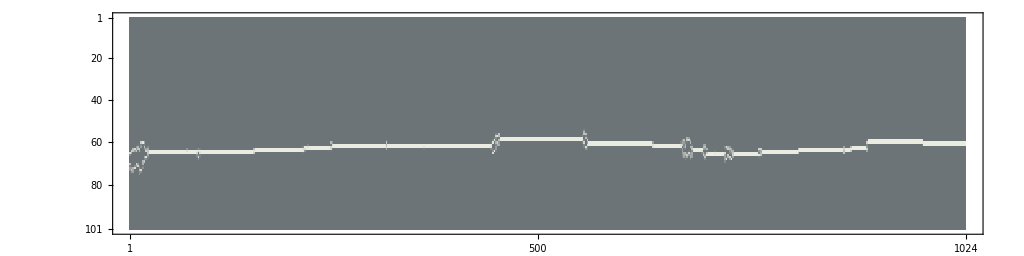

```mathematica
location = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest2/1024/0.01/";
nMax = 1;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[location<>ToString[i]<>"/typeStats.dat", "Data" ]; MatrixPlot[u[[400;;500,All]], ColorFunction->"GrayTones", ImageSize->{1024,256}]  //Print]
```

```mathematica
~
```

```mathematica
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest/1024/0.01/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/numBonds.dat", "Data" ]; ListPlot[u, PlotRange->{0.0, 1.0}] //Print]
```

```mathematica
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest/1024/0.01/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/extraInfo.dat", "Data" ]; dataTable[[i+1]] = {u[[1]][[1]], u[[1]][[3]]}];
ListPlot[dataTable]
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest/1024/0.1/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/extraInfo.dat", "Data" ]; dataTable[[i+1]] = {u[[1]][[1]], u[[1]][[3]]}];
ListPlot[dataTable]
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest/1024/0.5/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/extraInfo.dat", "Data" ]; dataTable[[i+1]] = {u[[1]][[1]], u[[1]][[3]]}];
ListPlot[dataTable]
```